```mathematica
?plot
```

Information::notfound: Symbol "plot" not found.

```mathematica
help
```

help

```mathematica
??Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

Attributes[Plot]={HoldAll,Protected,ReadProtected}
 
Options[Plot]={AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

```mathematica
?plot
```

Information::notfound: Symbol "plot" not found.

```mathematica
?Plot*
```

RowBox[{"Plot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a plot of StyleBox["f", "TI"] as a function of StyleBox["x", "TI"] from SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]] to SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]. 
RowBox[{"Plot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] plots several functions SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].

```mathematica
.10pi
```

.10pi

```mathematica
PI
```

PI

```mathematica
Pi
```

π

```mathematica
1/3
```

1/3

```mathematica
2^100
```

1267650600228229401496703205376

```mathematica
clear
```

clear

```mathematica
a=1
```

1

```mathematica
a
```

1



```mathematica
Plot[Sin[x],{x,0,2*Pi}]
```

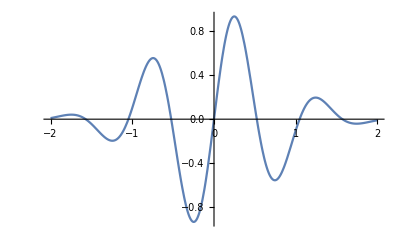

```mathematica
Plot[Exp[-x^2]*Sin[6*x],{x,-2,2}]
```

```mathematica
Plot3D[Sin[x*y],{x,-Pi,Pi},{y,-Pi,Pi}]
```

-Graphics3D-

```mathematica
Show[%2,%3]
```

Show::gcomb: Could not combine the graphics objects in Show[1, {Null}].

Show[1,{Null}]

```mathematica
Plot[Sin[x],{x,0,2*Pi}]
Plot[Exp[-x^2]*Sin[6*x],{x,-2,2}]
```

-Graphics-

-Graphics-

```mathematica
Plot[Sin[x],{x,0,2*Pi}]
Plot[Exp[-x^2]*Sin[6*x],{x,-2,2}]
Show[%1,%2]
```

-Graphics-

-Graphics-

Show::gcomb: Could not combine the graphics objects in Show[1, 1].

Show[1,1]

```mathematica
Range[1,2]
```

{1,2}

```mathematica
Range[1,10,0.1]
```

{1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2,6.3,6.4,6.5,6.6,6.7,6.8,6.9,7.,7.1,7.2,7.3,7.4,7.5,7.6,7.7,7.8,7.9,8.,8.1,8.2,8.3,8.4,8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9,10.}

```mathematica
Range[Range[1,10,1],0.1]
```

{{},{},{},{},{},{},{},{},{},{}}

```mathematica
Range[Range[1,2,1],0.1]
```

{{},{}}

```mathematica
Table[k^2,{k,1,5,1}]
```

{1,4,9,16,25}

```mathematica
Table[a^2,{a,1,5,1}]
```

{1,4,9,16,25}

```mathematica
Table[a+2*b,{a,1,5},{b,1,5}]
```

{{3,5,7,9,11},{4,6,8,10,12},{5,7,9,11,13},{6,8,10,12,14},{7,9,11,13,15}}

```mathematica
a=input["请输入半径："]
b=input["请输入姓名："]
```

```mathematica
input["请输入半径："]5
```

```mathematica
input["请输入姓名："]wangning
```

```mathematica
wangning input["请输入姓名："]wangning
```

```mathematica
wangning^2 input["请输入姓名："]2
```

2 wangning^2 input[请输入姓名：]

```mathematica
print["x+1",x+1]
```

```mathematica
x=2
```

2

```mathematica
Print["x + 1 = ",x+1]
```

x + 1 = 3

```mathematica
a=Input["请输入半径："]
b=Input["请输入姓名："]
```

3

wangning

```mathematica
b=2,a=1
Print[a+b,"\n",a-b]
```

Syntax::tsntxi: "b = 2, a = 1" is incomplete; more input is needed.""

```mathematica
b=2;a=1;
Print["a + b = ",a+b,"\n","a - b = ",a-b]
```

a + b = 3
a - b = -1

```mathematica
Solve[x^2==1,x]
```

Solve::ivar: 2 is not a valid variable.

Solve[False,2]

```mathematica
Solve[a*x^2-1==0,x]
```

Solve::ivar: 2 is not a valid variable.

Solve[False,2]

```mathematica
Slove[{x+y==3,x-y==1},{x,y}]
```

Slove[{2+y==3,2-y==1},{2,y}]

```mathematica
∫_1^2 Slove[{2+y==3,2-y==1},{2,y}]ⅆy
```

∫_1^2 Slove[{2+y==3,2-y==1},{2,y}]ⅆy

Integrate[Slove[{2 + y == 3, 2 - y == 1}, {2, y}], {y, 1, 2}]

WolframAlphaQueryResults

```mathematica
q
```

```mathematica
N[Pi,200]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930382